## Numerical Results for Neutrino Oscillations in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/assets

```mathematica
ClearAll[deltaH,numDen]
```

### Numerical

First of all I need to construct the function of solar electron number density.

#### Define Interpolation Function

```mathematica
numDen[x_]=10^(-14-4.3 x)
```

10^(-14-4.3 x)

```mathematica
numDen[0]
```

1.×10^-14

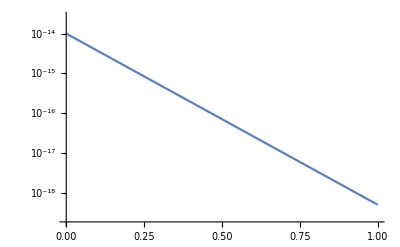

```mathematica
LogPlot[numDen[x],{x,0,1}]
```

Some useful constants
Fermi coupling constant G_F /(hbar c)    1.166 378 7(6)×10^−5 GeV−2

```mathematica
rS = 10^5;
omega=10^(-19);
(*rSomega=rS*omega;*)
rSomega=100
gF=1.17*10^(-5);
deltaH[x_] = Sqrt[2]gF numDen[x]/(omega)
thetaV=Pi/6;
```

100

0.0000165463 10^(5-4.3 x)

Hamiltonian is

```mathematica
hamilM[x_]=rSomega/2{{deltaH[x]-Cos[2thetaV],Sin[2thetaV]},{Sin[2thetaV],-deltaH[x]+Cos[2thetaV]}}
```

{{50 (-1/2+0.0000165463 10^(5-4.3 x)),25 √3},{25 √3,50 (1/2-0.0000165463 10^(5-4.3 x))}}

The function to be obtained is

```mathematica
nuM[x_]={nuMe[x],nuMx[x]}
```

{nuMe[x],nuMx[x]}

The system becomes

```mathematica
matOsc=I nuM'[x]==hamilM[x].nuM[x]
```

{ⅈ nuMe'[x],ⅈ nuMx'[x]}=={50 (-1/2+0.0000165463 10^(5-4.3 x)) nuMe[x]+25 √3 nuMx[x],25 √3 nuMe[x]+50 (1/2-0.0000165463 10^(5-4.3 x)) nuMx[x]}

```mathematica
solM=NDSolve[matOsc&&nuM[0]=={1,0},{nuMe,nuMx},{x,0,1}]
```

{{nuMe→InterpolatingFunction[{{0., 1.}}, <>],nuMx→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
probesqrt=nuMe/.solM[[1]]
probxsqrt=nuMx/.solM[[1]]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
Table[probesqrt[i],{i,0,1,0.1}]
probxsqrt[0]
```

{1.+0. ⅈ,0.484727+0.428144 ⅈ,-0.788945+0.0933212 ⅈ,-0.171328-0.228108 ⅈ,0.700299-0.10541 ⅈ,0.437482+0.152819 ⅈ,-0.469121+0.176267 ⅈ,-0.688507-0.0535605 ⅈ,0.0838412-0.20467 ⅈ,0.735082-0.0620453 ⅈ,0.332247+0.169304 ⅈ}

0.+0. ⅈ

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probxsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2

```mathematica
Table[norm[i],{i,0,1,0.1}]
```

{1.,0.999997,0.999997,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.}

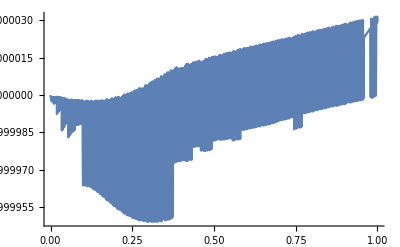

```mathematica
Plot[norm[x],{x,0,1}]
```

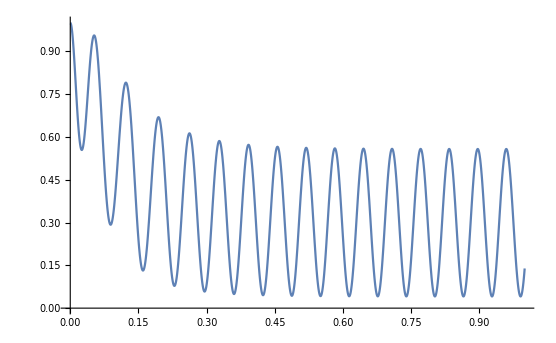

```mathematica
Plot[Abs[probesqrt[x]]^2/norm[x],{x,0,1}]
```

```mathematica
Abs[probesqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2